Ejercicio 3 a.

```mathematica
Subscript[F, x][x_]:= Piecewise[{{0,x<0},{x^2/16,0⩽x<2},{1/4,2⩽x<4},{(2x-5)/8,4⩽x<5},{1-5/(4x), x⩾5}}]
```

Usando la definición de función de distribución y de probabilidad condicionada, obtenemos la función de distribución de la variable truncada  mediante: .  En el numerador solo habrá probabilidad positiva cuando , mientras que en el denominador se tendrá

```mathematica
Subscript[F, z][z_]:=Piecewise[{{(Subscript[F, x][z]-Limit[Subscript[F, x][u],u->2,Direction->"FromBelow"])/(1-Limit[Subscript[F, x][u],u->2,Direction->"FromBelow"]),z>2}},0]
```

```mathematica
Subscript[F, z][z]//Simplify
```

Piecewise[{{1/6 (-7+2 z), 4≤z<5}, {1-5/(3 z), z≥5}, {0, True}}]

posee saltos en 4 y 5 (igual que )

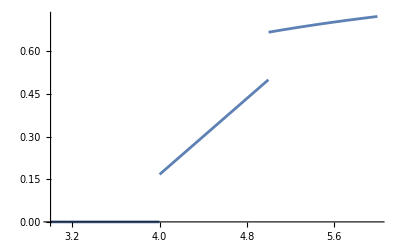

```mathematica
Plot[Evaluate@Subscript[F, z][z],{z,3,6}]
```

La probabilidad en los saltos suma:

```mathematica
Sum[Subscript[F, z][i]-Limit[Subscript[F, z][u],u->i,Direction->"FromBelow"],{i,4,5}]
```

1/3

Obtenemos la pseudodensidad derivando la función de distribución:

```mathematica
Subscript[f, z][z_]:=Derivative[1][Subscript[F, z]][z]
```

```mathematica
Subscript[f, z][z]//Simplify
```

Piecewise[{{1/3, 4<z<5}, {5/(3 z^2), z>5}, {0, z<4}, {Indeterminate, True}}]

```mathematica
Integrate[Subscript[f, z][z],{z,-Infinity,Infinity}]
```

2/3

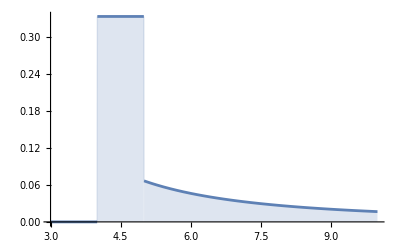

```mathematica
Plot[Evaluate@Subscript[f, z][z],{z,3,10},PlotRange->All,Filling->Bottom]
```

El área bajo la curva es . Esto, sumado a la masa total de  correspodiente a la parte discreta nos da 1 (como debe ser).

Ejercicio 3 b.

Para buscar la mediana (y otros) podemos obsevar la gráfica de la  función de distribución y cortar en 0.5 (y otros):

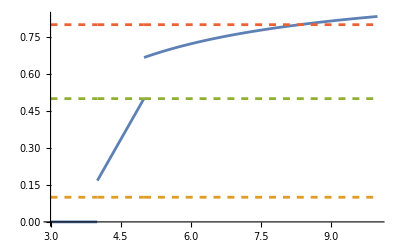

```mathematica
Plot[{Evaluate@Subscript[F, z][z],1/10,1/2,8/10},{z,3,10},PlotStyle->{{},{Dashed},{Dashed},{Dashed}}]
```

La mediana debe cumplir   . Claramente, . Del mismo modo se llega a . El percentil 80, en cambio, corta a una parte continua, por lo que debe hallarse resolviendo la ecuación . De ahí,

```mathematica
Solve[Subscript[F, z][z]==0.8,z]
```

{{z→8.33333}}

Ejercicio 4 a.

No es necesario, pero también puede definirse  en función de

```mathematica
F[x_,k_]:=Piecewise[{{0,x<0},{1/4+k x,0<=x<1},{2/3,1<=x<2},{x/4+k,2<=x<3},{1,x>=3}}]
```

Dado que  debe ser no decreciente, es claro que  y que, además, deben verificarse las siguientes condiciones:

```mathematica
Reduce[{Limit[F[x,k],x->1,Direction->"FromBelow"]<=2/3,2/3<=F[2,k],Limit[F[x,k],x->3,Direction->"FromBelow"]<=1},k]
```

1/6≤k≤1/4

Ejercicio 4 b.

Definimos la distribución de probabilidad asociada a  para

```mathematica
𝒟=ProbabilityDistribution[{"CDF",F[x,k]},{x,-Infinity,Infinity}]/.k->0.2
```

MixtureDistribution[{0.45,0.55},{ProbabilityDistribution[Piecewise[{{0.555556, 2≤x≤3}, {0.444444, 0≤x<1}, {0, True}}],{x,-∞,∞}],ProbabilityDistribution[Piecewise[{{0.454545, x==0}, {0.393939, x==1}, {0.0606061, x==2}, {0.0909091, x==3}, {0, True}}],{x,0,3,1}]}]

La esperanza se puede calcular como

```mathematica
Expectation[X,X\[Distributed]𝒟]
```

1.15833

También directamente con:

```mathematica
Subscript[m, 𝒟]=Mean[𝒟]
```

1.15833

```mathematica
Variance[𝒟]
```

1.10826

```mathematica
Median[𝒟]
```

1.

Por último, buscamos los valores   para  (con Chop se sustityen valores muy pequeños por 0, algo que puede suceder por razone de cálculo numérico)

```mathematica
Table[Expectation[(X-Subscript[m, 𝒟])^n,X\[Distributed]𝒟],{n,1,10}]//Chop
```

{0,1.10826,0.540439,2.16373,2.08248,5.20225,6.95012,14.2832,22.3848,42.4117}